Example of calculation of electron and electron scattering (Möller scattering)

**********************************************************************************************

1.Scattering of electrons and positrons using four γ matrices (4*4) (Meller scattering) (conventional calculation)

Center-of-mass scattering cross section (conventional calculation)；(do e1^4 (20 m^4+80 m^2 pu^2+99 pu^4+4 (3 m^4+12 m^2 pu^2+7 pu^4) Cos[2 θ]+pu^4 Cos[4 θ]) Csc[θ]^4)/(32 pu^4 (m^2+pu^2))

Scattering cross section in the ultra-relativistic case (conventional calculation)；1/64 α^2 (7+Cos[2 θ])^2 Csc[θ]^4

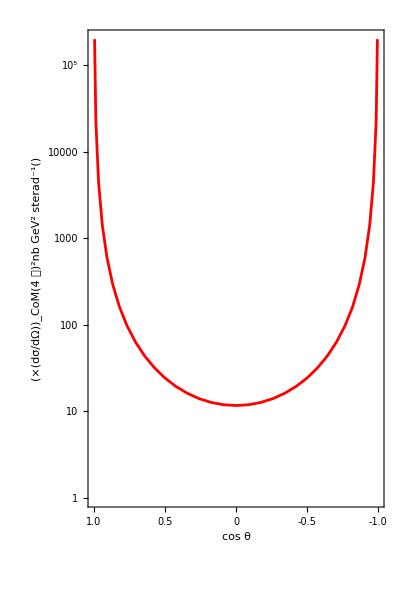

**********************************************************************************************

2.Scattering of electrons and positrons using γ matrix (256*256) (Möller scattering)

2.1.Calculation using 4 γ matrices (256*256) under Minkowski spacetime

Calculate the metric tensor as (-1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

det（Determinant of the metric tensor）=-1

(do e1^4 (20 m^4+80 m^2 pu^2+99 pu^4+4 (3 m^4+12 m^2 pu^2+7 pu^4) Cos[2 θ]+pu^4 Cos[4 θ]) Csc[θ]^4)/(512 pu^4 (m^2+pu^2))

Center-of-mass scattering cross section (conventional calculation)；(do e1^4 (20 m^4+80 m^2 pu^2+99 pu^4+4 (3 m^4+12 m^2 pu^2+7 pu^4) Cos[2 θ]+pu^4 Cos[4 θ]) Csc[θ]^4)/(512 pu^4 (m^2+pu^2))

Scattering cross section in the ultra-relativistic case (conventional calculation)；1/64 α^2 (7+Cos[2 θ])^2 Csc[θ]^4

**********************************************************************************************

2.2.Trial calculation example using 16 γ matrices (256*256) under curved space-time

Calculate the metric tensor as (-1 | 1/9 | 1/9 | 1/9
1/9 | 10/9 | 1/9 | 1/9
1/9 | 1/9 | 10/9 | 1/9
1/9 | 1/9 | 1/9 | 10/9)

det（Determinant of the metric tensor）=-37/27

Center-of-mass scattering cross section (conventional calculation)；1/(705277476864 pu^4 (m^2+pu^2)^3)do e1^4 (33291591971 m^8+212950936912 m^6 pu^2+533960529672 m^4 pu^4+573123425216 m^2 pu^6+219126989104 pu^8-13968800 m^4 pu^2 (m^2+pu^2) Cos[θ]+(21105753261 m^8+138302914992 m^6 pu^2+266595951352 m^4 pu^4+202967489856 m^2 pu^6+53662339664 pu^8) Cos[2 θ]+13968800 m^6 pu^2 Cos[3 θ]+13968800 m^4 pu^4 Cos[3 θ]+2323440000 m^4 pu^4 Cos[4 θ]+4646880000 m^2 pu^6 Cos[4 θ]+2323440000 pu^8 Cos[4 θ]) Csc[θ]^4

Scattering cross section in the ultra-relativistic case (calculation example using 16 γ matrices (256*256) in the case of curved space)；(α^2 (13695436819+3353896229 Cos[2 θ]+145215000 Cos[4 θ]) Csc[θ]^4)/11019960576

**********************************************************************************************

3.When using 4 γ matrices under Minkowski spacetime (conventional calculation) and γ matrix (256*256) under curved spacetime.
Comparison of trial calculation examples using 16 (trial calculation examples in this paper)

-Graphics-

```mathematica
(*Title:Møller Scattering Calculation (e⁻e⁻->e⁻e⁻) 
Author:[Hirokazu Maruyama] Date:January 2025 Version:1.0 Description:This code computes the Møller scattering cross section using:1. Conventional approach with 4x4 gamma matrices 2. Extended formalism with 256x256 gamma matrices 3. Implementation in both Minkowski and curved spacetime Physical Background:-Electron-electron scattering involves exchange diagrams-Features identical particle effects in final state-Shows characteristic angular distribution*)


(*Key Variables and Parameters:m-electron mass s,t,u-Mandelstam variables α-fine structure constant (1/137) θ-scattering angle E-electron energy in lab frame Matrix Definitions:gu[μ]-gamma matrices with upper index gd[μ]-gamma matrices with lower index sl[p]-Dirac slash notation for momentum p*)

(*Step 1:Define gamma matrices and spinor states*)(*Step 2:Calculate scattering amplitudes Note:Include both direct and exchange terms due to identical particles*)(*Step 3:Convert to center of mass frame coordinates*)(*Step 4:Compute differential cross section Note:Include 1/2 factor for identical particles in final state*)(*Step 5:Calculate angular distributions and compare between formalisms*)



(*Results Interpretation:-Angular distribution shows characteristic 1/sin⁴(θ/2) behavior-Cross section includes identical particle interference effects-Curved space calculation demonstrates[specific effects]*)


(*Plot Description:-X-axis:cos(θ) from-1 to 1-Y-axis:differential cross section (nb/GeV.b2/sr)-Red dashed line:conventional calculation result-Blue solid line:result in curved spacetime-Note:Asymmetry in angular distribution due to identical particle effects*)




Print[Style["Example of calculation of electron and electron scattering (Möller scattering)",Blue]];


Print["**********************************************************************************************"];
Print[Style["1.Scattering of electrons and positrons using four γ matrices (4*4) (Meller scattering) (conventional calculation)",Blue]];


m=.;
s=.;
t=.;
u=.;
dt=.;
pu=.;
ε=.;
θ=.;
re=.; 
α=.;

(*γ matrix(4×4)*)
γu[0]={{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}};
γu[1]={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
γu[2]={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
γu[3]={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
e4=IdentityMatrix[4];
ms=m*e4;

γd[0]=1*γu[0];
γd[1]=-γu[1];
γd[2]=-γu[2];
γd[3]=-γu[3];

sl[p]=γu[0]*p0+1*(γu[1]*(-p1)+γu[2]*(-p2)+γu[3]*(-p3)+ms);
sl[q]=γu[0]*q0+1*(γu[1]*(-q1)+γu[2]*(-q2)+γu[3]*(-q3)+ms);
sl[k]=γu[0]*k0+1*(γu[1]*(-k1)+γu[2]*(-k2)+γu[3]*(-k3)+ms);
sl[j]=γu[0]*j0+1*(γu[1]*(-j1)+γu[2]*(-j2)+γu[3]*(-j3)+ms);

ftu1=0;
gtu1=0;
fut1=0;
gut1=0;

y1=0;
y2=0;
y3=0;
y4=0;

For[x=0,x≤3,x++,
For[y=0,y≤3,y++,
ftu1=1/(16*t^2)*Tr[sl[j].γu[x].sl[k].γu[y]]*Tr[sl[q].γd[x].sl[p].γd[y]];
gtu1=-1/(16*t*u)*Tr[sl[j].γu[x].sl[k].γu[y].sl[q].γd[x].sl[p].γd[y]];
gut1=-1/(16*t*u)*Tr[sl[k].γu[x].sl[j].γu[y].sl[p].γd[x].sl[q].γd[y]];

y1=y1+FullSimplify[ExpandAll[ftu1]];
y3=y3+FullSimplify[ExpandAll[gtu1]];
y4=y4+FullSimplify[ExpandAll[gut1]];

]];


(*Conversion using Mandelstam variables*)

M=m;
T1=Simplify[y1//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];

T2=Simplify[T1//.{u->t}];

T3=Simplify[y3//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];
T4=Simplify[y4//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];

y5=T1+T2+T3+T4;

(*Center of gravity system*)

pu=.;
m=.;
ε=.;
θ=.;
t=4m^2-s-u;
s=4*(pu^2+m^2);
t=-4*pu^2*Sin[θ/2]^2;
u=-4*pu^2*Cos[θ/2]^2;

ε=Sqrt[pu^2+m^2];
jy=Pi*re^2*4*m1^2*dt/(s(s-4m^2));
re=e1^2/m1;
dt=pu^2*do/Pi;

y6=Simplify[jy*y5];
Print["Center-of-mass scattering cross section (conventional calculation)；",y6];

(*Cross section in ultra-relativistic case (conventional calculation)*)
y7=Simplify[y6//.{pu->ε,m->0,do->1,e1->1}];
yf1=4*ε^2*α^2*y7;
b=Extract[yf1,First@Position[yf1,α^2]-1]*64;
yf2=yf1/b;
Print["Scattering cross section in the ultra-relativistic case (conventional calculation)；",yf2];
x=Cos[θ];
α=1/137;
ListLogPlot[Table[{-x,yf2*(10^6/2.57)},{θ,Pi/36,Pi,Pi/36}],PlotStyle->Red,AspectRatio->1.5,Joined->True,Frame->{{True,None},{True,None}},FrameLabel->{"cos θ",Labeled[Subscript["×(dσ/dΩ)",CoM],{Superscript[4 Ｅ,2],Labeled[nb Superscript[GeV,2] Superscript[sterad,-1],{"(",")"},{Left,Right},Spacings->0.1]},{Left,Right},Spacings->0.1]},FrameTicks->{{{{10,Superscript[10,1]},{100,Superscript[10,2]},{1000,Superscript[10,3]},{10000,Superscript[10,4]},{100000,Superscript[10,5]}},None},
{{{-1,"1.0"},{-0.5,0.5},{0,0},{0.5,-0.5},{1,"-1.0"}},None}},PlotRange->{{-1,1},{1*^0,2*^5}},Axes->None]



Print["**********************************************************************************************"];


Print[Style["2.Scattering of electrons and positrons using γ matrix (256*256) (Möller scattering)",Blue]];

m=.;
s=.;
t=.;
u=.;
dt=.;
pu=.;
ε=.;
θ=.;
k=.;
α=.;
re=.; 


(*Find 16 combinations of gamma matrix (256 rows and 256 columns) that satisfy the anticommutation relationship*)
demoteRank4to2[y_]:=Flatten[Map[Flatten,Transpose[y,{1,3,2,4}],{2}],1];
pauli8times[g1_,g2_,g3_,g4_,g5_,g6_,g7_,g8_]:=demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,g1,g2]],demoteRank4to2[Outer[Times,g3,g4]]]],demoteRank4to2[Outer[Times,demoteRank4to2[Outer[Times,g5,g6]],demoteRank4to2[Outer[Times,g7,g8]]]]]];

g[1]={{0,1},{1,0}};
g[2]={{0,-I},{I,0}};
g[3]={{1,0},{0,-1}};
g[0]={{1,0},{0,1}};

e256=IdentityMatrix[256];


γuv[0]=pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[0],g[3]];
γuv[1]=I*pauli8times[g[0],g[0],g[0],g[0],g[3],g[2],g[2],g[2]];
γuv[2]=I*pauli8times[g[0],g[0],g[0],g[1],g[2],g[2],g[2],g[2]];
γuv[3]=I*pauli8times[g[0],g[0],g[3],g[2],g[2],g[2],g[2],g[2]];

γuv[4]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[0],g[1]];
γuv[5]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[3],g[2]];
γuv[6]=I*pauli8times[g[1],g[2],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[7]=I*pauli8times[g[0],g[0],g[1],g[2],g[2],g[2],g[2],g[2]];

γuv[8]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[3],g[2],g[2]];
γuv[9]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[0],g[1],g[2]];
γuv[10]=I*pauli8times[g[3],g[2],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[11]=I*pauli8times[g[0],g[0],g[0],g[0],g[1],g[2],g[2],g[2]];

γuv[12]=I*pauli8times[g[0],g[0],g[0],g[0],g[0],g[1],g[2],g[2]];
γuv[13]=I*pauli8times[g[0],g[1],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[14]=I*pauli8times[g[0],g[3],g[2],g[2],g[2],g[2],g[2],g[2]];
γuv[15]=I*pauli8times[g[0],g[0],g[0],g[3],g[2],g[2],g[2],g[2]];


num=115792089237316195423570985008687907853269984665640564039457584007913129639936;(*Determinant confirmation*)



(*16 γ matrices (256×256) Calculation to confirm that the anticommutative relationship is satisfied*)
yt=0;
For[kh=0,kh≤15,kh++,
For[ks1=0,ks1≤15,ks1++,
yf=Det[γuv[kh].γuv[ks1]+γuv[ks1].γuv[kh]];
yt=yf+yt;
If[kh=!=ks1 && yf==num*16,Print["No.",km,",x=",kh,",y=",ks1]];
]];

If[kh==16&& ks1==16 && yt/num==16,Print[""],Print["γ matrix (256*256) 16 pieces Anti-commutation relation confirmation　NG"]];

Print[Style["2.1.Calculation using 4 γ matrices (256*256) under Minkowski spacetime",Blue]];

gd1[0]=100;
gd1[1]=100;
gd1[2]=100;
gd1[3]=100;
gd1[4]=0;
gd1[5]=0;
gd1[6]=0;
gd1[7]=0;
gd1[8]=0;
gd1[9]=0;
gd1[10]=0;
gd1[11]=0;
gd1[12]=0;
gd1[13]=0;
gd1[14]=0;
gd1[15]=0;

m256=100*m;


(*γ matrix multiplied by metric*)

For[km1=0,km1≤15,km1++,
γu[km1]=gd1[km1]*γuv[km1];
];

For[km2=0,km2≤15,km2++,
γd[km2]=-1*γu[km2];
];
γd[0]=1*γu[0];

metric={{-gd1[0],gd1[10],gd1[12],gd1[14]},{gd1[11],gd1[1],gd1[4],gd1[6]},{gd1[13],gd1[5],gd1[2],gd1[8]},{gd1[15],gd1[7],gd1[9],gd1[3]}}/gd1[0];

Print["Calculate the metric tensor as ",MatrixForm[metric]];

Print["det（Determinant of the metric tensor）=",Det[metric]];



sl[q]=γu[0]*q0+γu[1]*-q1+γu[2]*-q2+γu[3]*-q3+m256*e256;
sl[p]=γu[0]*p0+γu[1]*-p1+γu[2]*-p2+γu[3]*-p3+m256*e256;
sl[k]=γu[0]*k0+γu[1]*-k1+γu[2]*-k2+γu[3]*-k3+m256*e256;
sl[j]=γu[0]*j0+γu[1]*-j1+γu[2]*-j2+γu[3]*-j3+m256*e256;



ftu10=0;
gtu10=0;
fut10=0;
gut10=0;

y10=0;
y20=0;
y30=0;
y40=0;


For[x=0,x≤3,x++,
For[y=0,y≤3,y++,
ftu10=1/(64*t^2)*Tr[sl[j].γu[x].sl[k].γu[y]]*Tr[sl[q].γd[x].sl[p].γd[y]];
gtu10=-1/(t*u)*Tr[sl[j].γu[x].sl[k].γu[y].sl[q].γd[x].sl[p].γd[y]];
gut10=-1/(t*u)*Tr[sl[k].γu[x].sl[j].γu[y].sl[p].γd[x].sl[q].γd[y]];

y10=y10+FullSimplify[ExpandAll[ftu10]];
y30=y30+FullSimplify[ExpandAll[gtu10]];
y40=y40+FullSimplify[ExpandAll[gut10]];

]];



(*Conversion using Mandelstam variables*)

m256=m;
M=m;
T10=Simplify[y10/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];

T20=Simplify[T10//.{u->t}];

T30=Simplify[y30/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];
T40=Simplify[y40/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];

y50=T10+T20+T30+T40;



(*Center of gravity system*)
pu=.;
m=.;
ε=.;
θ=.;
t=4m^2-s-u;
s=4*(pu^2+m^2);
t=-4*pu^2*Sin[θ/2]^2;
u=-4*pu^2*Cos[θ/2]^2;

ε=Sqrt[pu^2+m^2];
jy=Pi*re^2*4*m1^2*dt/(s(s-4m^2));
re=e1^2/m1;
dt=pu^2*do/Pi;
bf100=16*1024*gd1[0]^8;
y60=Simplify[jy*y50];
yf61=y60/bf100;
Print[yf61];

Print["Center-of-mass scattering cross section (conventional calculation)；",yf61];


(*Cross section in ultra-relativistic case (conventional calculation)*)
y70=Simplify[y60//.{pu->ε,m->0,do->1,e1->1}];
yf10=4*ε^2*α^2*y70;
bf10=16*1024*gd1[0]^8;
yf20=yf10/bf10;
Print["Scattering cross section in the ultra-relativistic case (conventional calculation)；",yf20];



Print["**********************************************************************************************"];

Print[Style["2.2.Trial calculation example using 16 γ matrices (256*256) under curved space-time",Blue]];

m=.;
s=.;
t=.;
u=.;
dt=.;
pu=.;
ε=.;
θ=.;
k=.;
α=.;


(*Set metric tensor*)


gd2[0]=9/10;
gd2[1]=1;
gd2[2]=1;
gd2[3]=1;
gd2[4]=1/10;
gd2[5]=1/10;
gd2[6]=1/10;
gd2[7]=1/10;
gd2[8]=1/10;
gd2[9]=1/10;
gd2[10]=1/10;
gd2[11]=1/10;
gd2[12]=1/10;
gd2[13]=1/10;
gd2[14]=1/10;
gd2[15]=1/10;

m256=1*m;



(*γ matrix multiplied by metric*)

For[km1=0,km1≤15,km1++,
γu[km1]=gd2[km1]*γuv[km1];
];


For[km2=0,km2≤15,km2++,
γd[km2]=-1*γu[km2];
];
γd[0]=1*γu[0];

metric={{-gd2[0],gd2[10],gd2[12],gd2[14]},{gd2[11],gd2[1],gd2[4],gd2[6]},{gd2[13],gd2[5],gd2[2],gd2[8]},{gd2[15],gd2[7],gd2[9],gd2[3]}}/gd2[0];


Print["Calculate the metric tensor as ",MatrixForm[metric]];

Print["det（Determinant of the metric tensor）=",Det[metric]];

sl[q]=γu[0]*q0+γu[1]*-q1+γu[2]*-q2+γu[3]*-q3+m256*e256;
sl[p]=γu[0]*p0+γu[1]*-p1+γu[2]*-p2+γu[3]*-p3+m256*e256;
sl[k]=γu[0]*k0+γu[1]*-k1+γu[2]*-k2+γu[3]*-k3+m256*e256;
sl[j]=γu[0]*j0+γu[1]*-j1+γu[2]*-j2+γu[3]*-j3+m256*e256;

ftu100=0;
gtu100=0;
fut100=0;
gut100=0;

y100=0;
y200=0;
y300=0;
y400=0;



For[x=0,x≤15,x++,
For[y=0,y≤15,y++,
ftu100=1/(64*t^2)*Tr[sl[j].γu[x].sl[k].γu[y]]*Tr[sl[q].γd[x].sl[p].γd[y]];
gtu100=-1/(t*u)*Tr[sl[j].γu[x].sl[k].γu[y].sl[q].γd[x].sl[p].γd[y]];
gut100=-1/(t*u)*Tr[sl[k].γu[x].sl[j].γu[y].sl[p].γd[x].sl[q].γd[y]];

y100=y100+FullSimplify[ExpandAll[ftu100]];
y300=y300+FullSimplify[ExpandAll[gtu100]];
y400=y400+FullSimplify[ExpandAll[gut100]];

]];


m256=m;

(*Conversion using Mandelstam variables*)

M=m;
T100=Simplify[y100/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];

T200=Simplify[T100//.{u->t}];

T300=Simplify[y300/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];
T400=Simplify[y400/((m256/m)^8)//.{p1->0,p2->0,k0->p3,k1->0,k2->0,k3->-p3,q0->p0,q1->p3*Sqrt[1-z^2],q2->0,q3->p3*z,j0->p3,j1->-p3*Sqrt[1-z^2],j2->0,j3->-p3*z,p0->(s+m^2+M^2)/(2 Sqrt[s]),p3->(s-m^2-M^2)/(2 Sqrt[s]),z->1+t/(2 p3^2),t->2 *(m^2+M^2)-s-u},TimeConstraint->5000];

y500=T100+T200+T300+T400;




(*Center of gravity system*)

t=4m^2-s-u;
s=4*(pu^2+m^2);
t=-4*pu^2*Sin[θ/2]^2;
u=-4*pu^2*Cos[θ/2]^2;
ε=Sqrt[pu^2+m^2];
jt=Pi*re^2*4*m1^2*dt/(s(s-4m^2));
re=e1^2/m1;
dt=pu^2*do/Pi;

bf100=16*1024*gd2[0]^8;
y600=Simplify[jt*y500];
yf601=y600/bf100;


Print["Center-of-mass scattering cross section (conventional calculation)；",yf601];

(*Cross section in ultra-relativistic case*)
y700=Simplify[y600//.{pu->ε,m->0,do->1,e1->1}];
yf100=4*ε^2*α^2*y700;

yf200=yf100/bf100;

Print["Scattering cross section in the ultra-relativistic case (calculation example using 16 γ matrices (256*256) in the case of curved space)；",yf200];


Print["**********************************************************************************************"];

x=Cos[θ];
α=1/137;
data1=Table[{-x,yf20*(10^6/2.57)},{θ,Pi/37,Pi,Pi/37}];
data2=Table[{-x,yf200*(10^6/2.57)},{θ,Pi/37,Pi,Pi/37}];


Print[Style["3.When using 4 γ matrices under Minkowski spacetime (conventional calculation) and γ matrix (256*256) under curved spacetime.
Comparison of trial calculation examples using 16 (trial calculation examples in this paper)",Blue]];

ListLogPlot[{data1,data2},PlotStyle->{{Red,Dashed},Blue},AspectRatio->1.5,Joined->True,Frame->{{True,None},{True,None}},
PlotLegends->Placed[LineLegend[Automatic,{"Conventional calculation","Example of calculation for this paper"},LabelStyle->8,
LegendFunction->"Frame",LegendLayout->"Column"],{{1,0.15},{1.15,0.075}}],
FrameLabel->{"cos θ",Labeled[Subscript["×(dσ/dΩ)",CoM],{Superscript[4 Ｅ,2],
Labeled[nb Superscript[GeV,2] Superscript[sterad,-1],{"(",")"},{Left,Right},Spacings->0.1]},{Left,Right},Spacings->0.1]},FrameTicks->{{{{10,Superscript[10,1]},{100,Superscript[10,2]},{1000,Superscript[10,3]},{10000,Superscript[10,4]},{100000,Superscript[10,5]}},None},
{{{-1,"1.0"},{-0.5,0.5},{0,0},{0.5,-0.5},{1,"-1.0"}},None}},PlotRange->{{-1,1},{1*^0,2*^5}},Axes->None]
```